```mathematica
Needs["WSMLink`"]
```

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}]
```

```mathematica
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["EFieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]]
```

```mathematica
mR1 = multipleEfieldLineSims[0,0,0.25,20]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 21.3044"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
dmR1=Dimensions[mR1][[1]]
```

21

```mathematica
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 21.3044}}, <>],InterpolatingFunction[{{0., 15.2633}}, <>],InterpolatingFunction[{{0., 11.9114}}, <>],InterpolatingFunction[{{0., 10.022}}, <>],InterpolatingFunction[{{0., 9.04696}}, <>],InterpolatingFunction[{{0., 8.74495}}, <>],InterpolatingFunction[{{0., 9.04696}}, <>],InterpolatingFunction[{{0., 10.022}}, <>],InterpolatingFunction[{{0., 11.9114}}, <>],InterpolatingFunction[{{0., 15.2633}}, <>],InterpolatingFunction[{{0., 21.3044}}, <>],InterpolatingFunction[{{0., 33.0581}}, <>],InterpolatingFunction[{{0., 59.4602}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 59.4602}}, <>],InterpolatingFunction[{{0., 33.0581}}, <>],InterpolatingFunction[{{0., 21.3044}}, <>]}

```mathematica
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 21.3044}}, <>],InterpolatingFunction[{{0., 15.2633}}, <>],InterpolatingFunction[{{0., 11.9114}}, <>],InterpolatingFunction[{{0., 10.022}}, <>],InterpolatingFunction[{{0., 9.04696}}, <>],Function[t,0.,Listable],InterpolatingFunction[{{0., 9.04696}}, <>],InterpolatingFunction[{{0., 10.022}}, <>],InterpolatingFunction[{{0., 11.9114}}, <>],InterpolatingFunction[{{0., 15.2633}}, <>],InterpolatingFunction[{{0., 21.3044}}, <>],InterpolatingFunction[{{0., 33.0581}}, <>],InterpolatingFunction[{{0., 59.4602}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],Function[t,0.,Listable],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 59.4602}}, <>],InterpolatingFunction[{{0., 33.0581}}, <>],InterpolatingFunction[{{0., 21.3044}}, <>]}

```mathematica
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]]
```

```mathematica
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}]
```

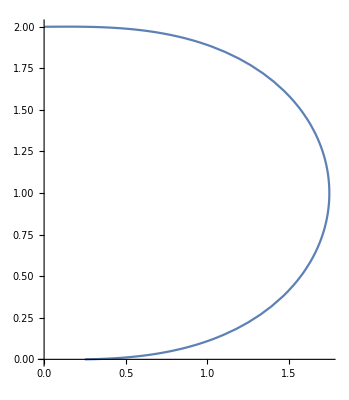
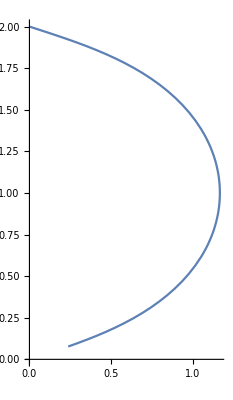
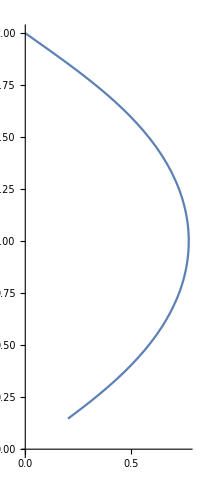
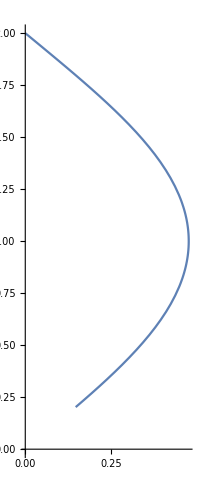
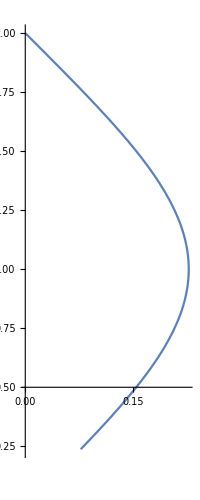
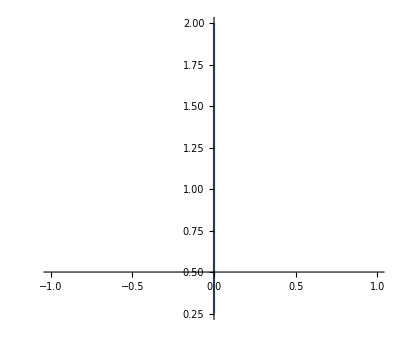
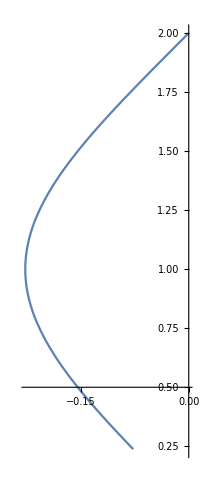
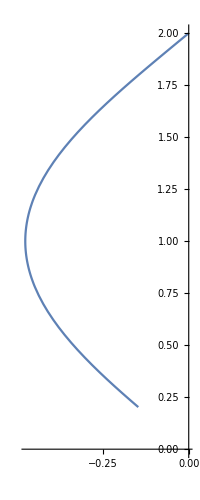
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
results=Table[EpPlot[i],{i,1,dmR1}]
```

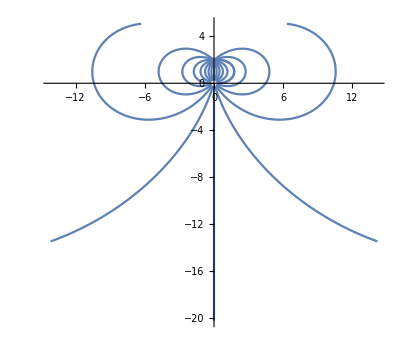

```mathematica
Show[results,PlotRange->All]
```

```mathematica
results=Table[EpPlot[i],{i,1,dmR1}];
```

```mathematica
Show[results,PlotRange->All]
```

-Graphics-